```mathematica
Cost of computation
```

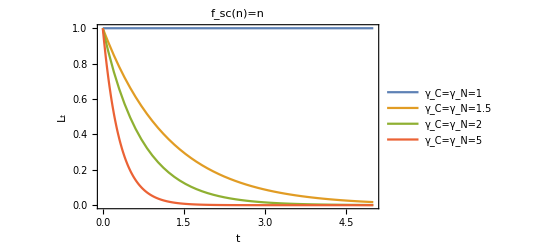

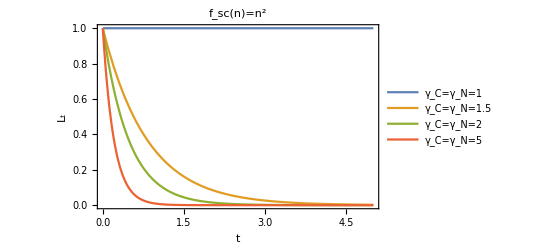

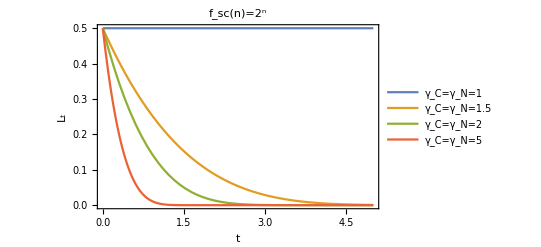

```mathematica
Plot[{gammaC^-t/gammaN^t /. {gammaC->1,gammaN->1},gammaC^-t/gammaN^t /. {gammaC->1.5,gammaN->1.5},gammaC^-t/gammaN^t /. {gammaC->2,gammaN->2},gammaC^-t/gammaN^t /. {gammaC->5,gammaN->5}},{t,0,5},PlotRange->All,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{"t","L_t"},PlotLegends->Placed[{"γ_C=γ_N=1","γ_C=γ_N=1.5","γ_C=γ_N=2","γ_C=γ_N=5"},{Right,Center}],PlotLabel->"f_sc(n)=n"]
Plot[{gammaC^-t/((gammaN^t)^2) /. {gammaC->1,gammaN->1},gammaC^-t/((gammaN^t)^2) /. {gammaC->1.5,gammaN->1.5},gammaC^-t/((gammaN^t)^2) /. {gammaC->2,gammaN->2},gammaC^-t/((gammaN^t)^2) /. {gammaC->5,gammaN->5}},{t,0,5},PlotRange->All,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{"t","L_t"},PlotLegends->Placed[{"γ_C=γ_N=1","γ_C=γ_N=1.5","γ_C=γ_N=2","γ_C=γ_N=5"},{Right,Center}],PlotLabel->"f_sc(n)=n^2"]
Plot[{gammaC^-t/(2^(gammaN^t)) /. {gammaC->1,gammaN->1},gammaC^-t/(2^(gammaN^t)) /. {gammaC->1.5,gammaN->1.5},gammaC^-t/(2^(gammaN^t)) /. {gammaC->2,gammaN->2},gammaC^-t/(2^(gammaN^t)) /. {gammaC->5,gammaN->5}},{t,0,5},PlotRange->All,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{"t","L_t"},PlotLegends->Placed[{"γ_C=γ_N=1","γ_C=γ_N=1.5","γ_C=γ_N=2","γ_C=γ_N=5"},{Right,Center}],PlotLabel->"f_sc(n)=2^n"]
```

### Single qubit QCL

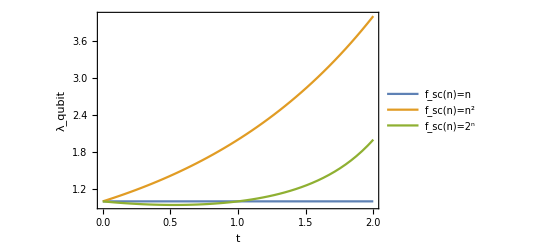

```mathematica
Plot[{gamma^t/gamma^t /. gamma->2,((gamma^t)^2)/gamma^t /.gamma->2,(2^(gamma^t))/(2 gamma^t) /. gamma->2},{t,0,2},PlotRange->All,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{"t","λ_qubit"},PlotLegends->Placed[{"f_sc(n)=n","f_sc(n)=n^2","f_sc(n)=2^n"},{Left,Center}]]
```

### Qubit asset pricing model

```mathematica
Plot3D[(ⅇ^r γ)/(ⅇ^r γ-1),{r,1,3},{γ,1,3},PlotRange->All,BaseStyle->{FontSize->14},AxesLabel->{"r","γ_C","S_0"}]
```

-Graphics3D-

### Forward contract pricing model

```mathematica
Plot3D[(ⅇ^(-r T)γ^-T)/(ⅇ^r γ-1)/. r->2,{T,0,2},{γ,1,3},PlotRange->All,BaseStyle->{FontSize->14},AxesLabel->{"T","γ_C","F(T)"},PlotLabel->"r=2"]
```

-Graphics3D-

### ROI

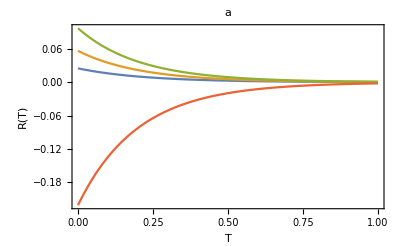

```mathematica
Plot[{ⅇ^(-r(T+1))/(ⅇ^(r(T+1))-gammaC^(T+1)) /. {r->2,gammaC->2},ⅇ^(-r(T+1))/(ⅇ^(r(T+1))-gammaC^(T+1)) /. {r->2,gammaC->5},ⅇ^(-r(T+1))/(ⅇ^(r(T+1))-gammaC^(T+1)) /. {r->2,gammaC->6},ⅇ^(-r(T+1))/(ⅇ^(r(T+1))-gammaC^(T+1)) /. {r->2,gammaC->8}},{T,0,1},PlotRange->All,Frame->True,BaseStyle->{FontSize->14},FrameLabel->{"T","R(T)"},PlotLegends->Placed[{},{Right,Center}],PlotLabel->"a"]
```

```mathematica
FullSimplify[Solve[ⅇ^(-r(T+1))/(ⅇ^(r(T+1))-γ^(T+1))==1,γ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ→2^(1/(1+T)) Sinh[r (1+T)]^(1/(1+T))}}